## Part 1. T(ϕ) = T_1

1.Calculation of A_n

```mathematica
An[n_]=(4*n+1)*1/(a^(2*n)-b^(4*n+1)*a^(-(2*n+1)))*T*(∫_0^(π/2) LegendreP[2*n,Cos[ϕ]]*Sin[ϕ]ⅆϕ)
```

(36 (LegendreP[-1+2 n,0]-LegendreP[1+2 n,0]))/(1-2^(1+4 n))

2. Check for the coefficients

```mathematica
Anvector=Table[An[n],{n,0,10}]
```

{-36,0,0,0,0,0,0,0,0,0,0}

3. Plot of u_trial(ρ , 0) and Contour plot for u_Trial(ρ, ϕ)

```mathematica
a=1(* m *)
b=2(* m *)
T=36(* °C *)
u1[ρ_,ϕ_]:=T/(1/b-1/a)*(1/b-1/ρ)
Plot[{u1[a,ϕ],u1[(a+b)/2,ϕ],u1[b,ϕ]},{ϕ,0,π/2},BaseStyle->{FontSize->18},AxesLabel->{"ϕ","u(ρ,ϕ)"},PlotStyle->Thick,PlotLegends->{"ρ=a","ρ=(a + b)/2","ρ=b"},PlotRange->All]
Plot[{u1[ρ,0]},{ρ,a,b},BaseStyle->{FontSize->18},AxesLabel->{"ρ","u(ρ,0)"},PlotStyle->Thick]
ContourPlot[u1[√(x^2+z^2),ArcTan[z,x]],{x,-b,b},{z,0,b},AspectRatio->0.5,RegionFunction->(a^2<#1^2+#2^2<b^2&),ColorFunction->"DarkRainbow",BaseStyle->{FontSize->18},FrameLabel->{"x","z"},Contours->Range[0,36,4],PlotLegends->Automatic]
```

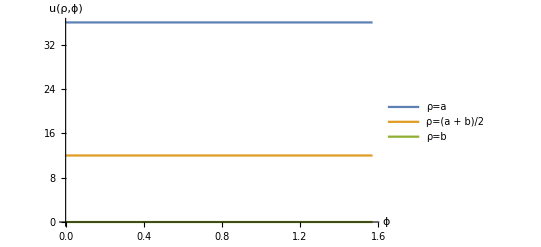

Addition plot to check if the BC and constrain are satisfied.

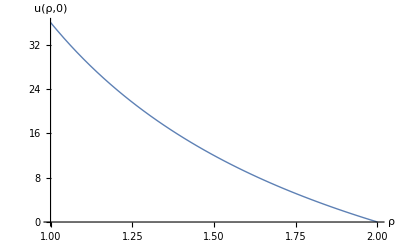

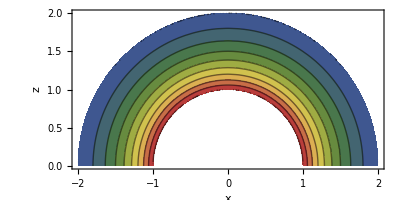

## Part 2. T(ϕ) =T_Final(ϕ)=AP_4(cos ϕ)+BP_6(cos ϕ)(in which A and B are constants)

1.Calculation and check of A_n

```mathematica
An1[n_]=(4*n+1)*1/(a^(2*n)-b^(4*n+1)*a^(-(2*n+1)))*(∫_0^(π/2) (A*LegendreP[4,Cos[ϕ]] +B*LegendreP[6,Cos[ϕ]])*LegendreP[2*n,Cos[ϕ]]*Sin[ϕ]ⅆϕ)
Anvector=Table[An1[n],{n,0,10}]
```

((-1+n) n (1+4 n) (5 B (-2+n) (5+2 n)-6 A (-3+n) (7+2 n)) √π)/(16 (a^(2 n)-a^(-1-2 n) b^(1+4 n)) (5+2 n) (7+2 n) Gamma[4-n] Gamma[1/2+n])

{0,0,A/(a^4-b^9/a^5),B/(a^6-b^13/a^7),0,0,0,0,0,0,0}

2. Calculation of constant A and B

```mathematica
a:=1;b:=2;
Solve[{A/(a^4-b^9/a^5)*(((a+b)/2)^4-b^9*((a+b)/2)^-5)+B/(a^6-b^13/a^7)*(((a+b)/2)^6-b^13*((a+b)/2)^-7)==12,A/(a^4-b^9/a^5)*(((a+b)/2)^4-b^9*((a+b)/2)^-5)*LegendreP[4,Cos[π/4]]+B/(a^6-b^13/a^7)*(((a+b)/2)^6-b^13*((a+b)/2)^-7)*LegendreP[6,Cos[π/4]]==6},{A,B}]
```

```mathematica
N[{{A->-659606976/2667071,B->531965740032/720659951}}]
```

{{A→-247.315,B→738.165}}

3. Plot of u_Final(a+b/2 , ϕ) and T_Final(ρ, ϕ)

(161352 (-512/ρ^5+ρ^4) (3-30 Cos[ϕ]^2+35 Cos[ϕ]^4))/2667071-(4059072 (-8192/ρ^7+ρ^6) (-5+105 Cos[ϕ]^2-315 Cos[ϕ]^4+231 Cos[ϕ]^6))/720659951

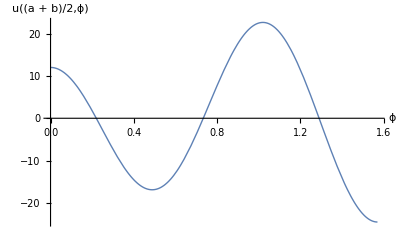

```mathematica
A:=-659606976/2667071;
B:=531965740032/720659951;
a:=1;
b:=2;
u2[ρ_,ϕ_]=A/(a^4-b^9/a^5)*(ρ^4-b^9*ρ^-5)*LegendreP[4,Cos[ϕ]]+
B/(a^6-b^13/a^7)*(ρ^6-b^13*ρ^-7)*LegendreP[6,Cos[ϕ]]
Plot[{u2[(a+b)/2,ϕ]},{ϕ,0,π/2},BaseStyle->{FontSize->18},AxesLabel->{"ϕ","u((a + b)/2,ϕ)"},PlotStyle->Thick,PlotRange->All]
```

4. Check if the constrains are satisfied

```mathematica
u2[(a+b)/2,π/4]
u2[(a+b)/2,0]
```

6

12

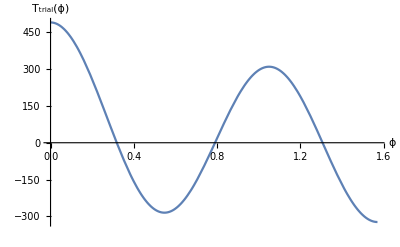

```mathematica
uT[ϕ_]:=A*LegendreP[4,Cos[ϕ]]+B*LegendreP[6,Cos[ϕ]]
Plot[uT[ϕ],{ϕ,0,π/2},BaseStyle->{FontSize->18},AxesLabel->{"ϕ","T_trial(ϕ)"},PlotRange->All]
```

5. Contour plot for u_Final(ρ, ϕ)

```mathematica
ContourPlot[u2[√(x^2+z^2),ArcTan[z,x]],{x,-b,b},{z,0,b},AspectRatio->0.5,RegionFunction->(a^2<#1^2+#2^2<b^2&),ColorFunction->"DarkRainbow",BaseStyle->{FontSize->18},FrameLabel->{"x","z"},Contours->Range[-260,440,20],PlotLegends->Automatic,PlotRange->All,ContourLabels->False]
```

-Graphics-

## Part 3. Unique Problem(u(ρ,π/2)=0; T(ϕ) =T_Final(ϕ)=CP_1(cos ϕ)+DP_3(cos ϕ)(in which C and D are constants)

1.Calculation and check of A_n

```mathematica
An2[n_]=(4*n-1)*1/(a^(-2*n)-b^(-4*n+1)*a^(2*n-1))*(∫_0^(π/2) (C*LegendreP[1,Cos[ϕ]] +D*LegendreP[3,Cos[ϕ]])*LegendreP[2*n-1,Cos[ϕ]]*Sin[ϕ]ⅆϕ)
Anvector=Table[An2[n],{n,1,10}]
```

((-1+4 n) (3 D (-1+n) (1+2 n)+2 C (6+n-2 n^2)) √π)/(16 (a^(-2 n)-a^(-1+2 n) b^(1-4 n)) Gamma[3-n] Gamma[5/2+n])

{C/(1/a^2-a/b^3),D/(1/a^4-a^3/b^7),0,0,0,0,0,0,0,0}

2. Calculation of constant C and D

```mathematica
a:=1;b:=2;
Solve[{C/(1/a^2-a/b^3)*(((a+b)/2)^-2-b^-3*((a+b)/2)^1)+D/(1/a^4-a^3/b^7)*(((a+b)/2)^-4-b^-7*((a+b)/2)^3)==12,C/(1/a^2-a/b^3)*(((a+b)/2)^-2-b^-3*((a+b)/2)^1)*LegendreP[1,Cos[π/4]]+D/(1/a^4-a^3/b^7)*(((a+b)/2)^-4-b^-7*((a+b)/2)^3)*LegendreP[3,Cos[π/4]]==6},{C,D}]
```

{{C→1512/185 (1+2 √2),D→-(1975104 (-2+√2))/70985}}

```mathematica
N[{{C->1512/185 (1+2 √2),D->-(1975104 (-2+√2))/70985}}]
```

{{C→31.2896,D→16.2991}}

3. Plot of u_Final(a+b/2 , ϕ) and T_Final(ρ, ϕ)

1728/185 (1+2 √2) (1/ρ^2-ρ/8) Cos[ϕ]-(995328 (-2+√2) (1/ρ^4-ρ^3/128) (-3 Cos[ϕ]+5 Cos[ϕ]^3))/70985

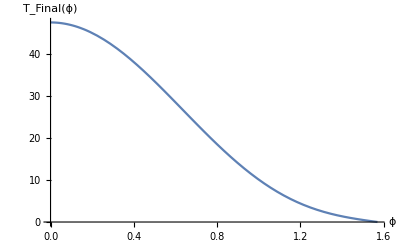

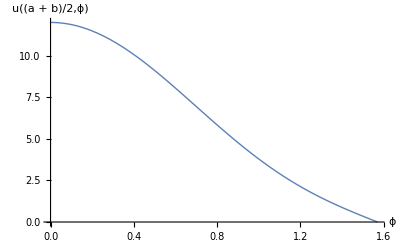

```mathematica
C1:=1512/185 (1+2 √2);
D1:=-(1975104 (-2+√2))/70985
a:=1;
b:=2;
u3[ρ_,ϕ_]=C1/(1/a^2-a/b^3)*(ρ^-2-b^-3*ρ^1)*LegendreP[1,Cos[ϕ]]+
D1/(1/a^4-a^3/b^7)*(ρ^-4-b^-7*ρ^3)*LegendreP[3,Cos[ϕ]]
uT1[ϕ_]:=C1*LegendreP[1,Cos[ϕ]]+D1*LegendreP[3,Cos[ϕ]]
Plot[uT1[ϕ],{ϕ,0,π/2},BaseStyle->{FontSize->18},AxesLabel->{"ϕ","T_Final(ϕ)"},PlotRange->All]
Plot[{u3[(a+b)/2,ϕ]},{ϕ,0,π/2},BaseStyle->{FontSize->18},AxesLabel->{"ϕ","u((a + b)/2,ϕ)"},PlotStyle->Thick,PlotRange->All]
```

4. Check if the constrains are satisfied

```mathematica
u3[(a+b)/2,π/4]
```

3/5 √2 (-2+√2)+6/5 √2 (1+2 √2)

```mathematica
N[3/5 √2 (-2+√2)+6/5 √2 (1+2 √2)]
```

6.

```mathematica
u3[(a+b)/2,0]
```

-24/5 (-2+√2)+12/5 (1+2 √2)

```mathematica
N[-24/5 (-2+√2)+12/5 (1+2 √2)]
```

12.

5. Contour plot for u_Final(ρ, ϕ)

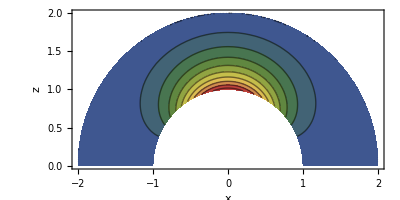

```mathematica
ContourPlot[u3[√(x^2+z^2),ArcTan[z,x]],{x,-b,b},{z,0,b},AspectRatio->0.5,RegionFunction->(a^2<#1^2+#2^2<b^2&),ColorFunction->"DarkRainbow",BaseStyle->{FontSize->18},FrameLabel->{"x","z"},Contours->Range[0,50,5],PlotLegends->Automatic,PlotRange->All,ContourLabels->False]
```